```mathematica
<<LevelScheme`CustomTicks`
```

Get::noopen: Cannot open "LevelScheme`CustomTicks`".

$Failed

## Pre-calc

```mathematica
Clear[H,h,c,m,b]
FullSimplify[Solve[{c H-(m H^2)/2==1,(c+b)(H/2-h)==1,(c-m H+b)(H/2+h)==1},{c,m,b}]]
```

{{c→1/H-(4 h)/(4 h^2-H^2),m→(8 h)/(-4 h^2 H+H^3),b→(4 h^2+H^2)/(-4 h^2 H+H^3)}}

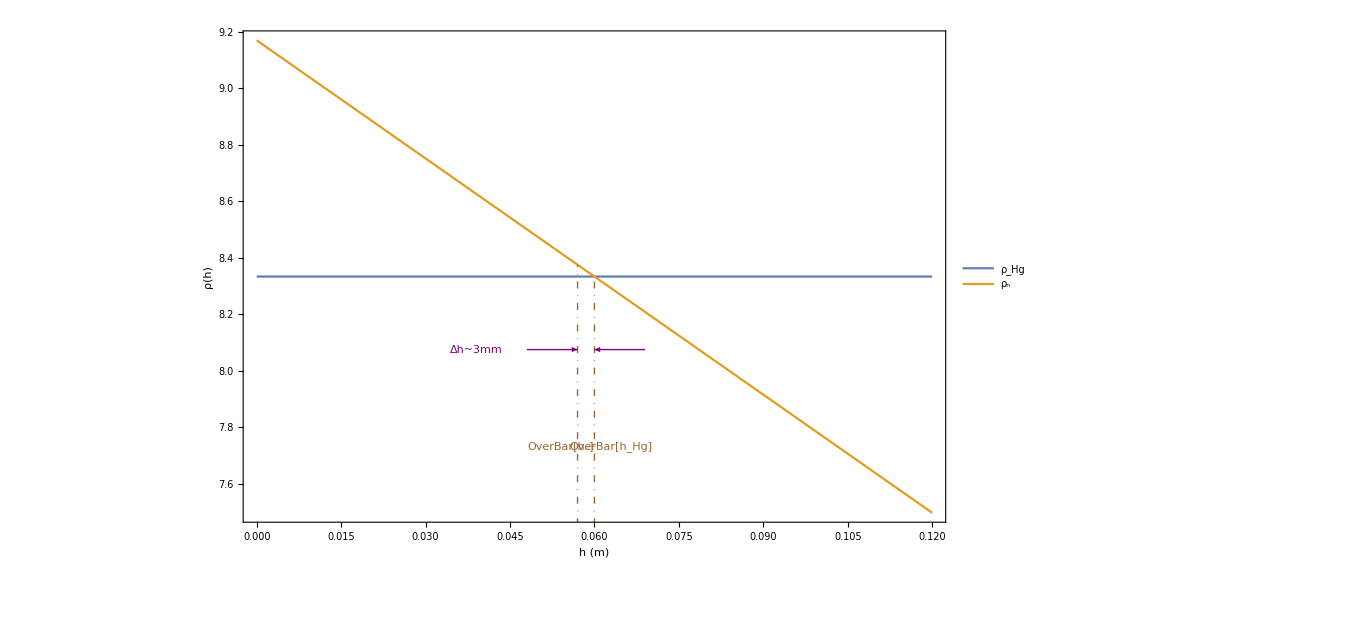

```mathematica
H=.12;h=.0054;b=(4 h^2+H^2)/(-4 h^2 H+H^3);
rhoHg[z_]=1/H;
rhon[z_]=(1/H-(4 h)/(4 h^2-H^2))-(8 h)/(-4 h^2 H+H^3)z;
lineStyle={Thick,Brown,DotDashed};
lineStyle5={Thick,Purple};
line1=Line[{{H/2,0},{H/2,1/H}}];
line2=Line[{{H/2-h,0},{H/2-h,b}}];
Plot[{rhoHg[z],rhon[z]},{z,0,H},PlotStyle->Thick,Frame->True,FrameLabel->{"h (m)","ρ(h)"},PlotLegends->{"ρ_Hg","ρ_n"},FrameTicksStyle->Thick,Frame->True,FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,Epilog->{
{Directive[lineStyle],line1,line2,Text[Style["OverBar[h_n]",FontSize->Large],{H/2-2h,1/H-200h}],Text[Style["OverBar[h_Hg]",FontSize->Large],{H/2+h,1/H-200h}]},
{Directive[lineStyle5],{Arrowheads[{0,0.02}],Arrow[{{H/2-4h,b-100h},{H/2-h,b-100h}}]},{Arrowheads[{0,0.02}],Arrow[{{H/2+3h,b-100h},{H/2,b-100h}}]},Text[Style["Δh~3mm",FontSize->Large],{H/2-7h,b-100h}]},
}]
```